```mathematica
FactInteger[n_]:=If[n==1,{},FactorInteger[n]]
d[n_,z_]:=Product[1/(p[[2]]!) Pochhammer[z,p[[2]]],{p,FactInteger[n]}]
```

```mathematica
pk[n_,0]:=pk[n,0]=If[n==1,1,0]
pk[n_,1]:=pk[n,1]=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
pk[n_,k_]:=pk[n,k]=Sum[pk[j,k-1]pk[n/j,1],{j,Divisors[n]}]
dv2[n_,k_]:=Sum[k^j/(j!) pk[n,j],{j,0,N[Log[n]/Log[2]]}]
dv3[n_,k_] := dv3[n,k]=pk[n,0]+k pk[n,1] + k^2/2 pk[n,2] + k^3/6 pk[n,3] + k^4/24 pk[n,4] + k^5 / 120 pk[n,5] + k^6/720 pk[n,6] + k^7/(7!) pk[n,7] + k^8/(8!) pk[n,8]
cosp[n_,k_] := cosp[n,k]= pk[n,0]- k^2/2 pk[n,2] + k^4/24 pk[n,4] - k^6/720 pk[n,6] + k^8/(8!) pk[n,8]
sinp[n_,k_] := sinp[n,k]=k pk[n,1] - k^3/6 pk[n,3] + k^5 / 120 pk[n,5] -  k^7/(7!) pk[n,7]
```

```mathematica
Table[{n,a=dv3[n,3I], b=(cosp[n,3]+I sinp[n,3]),a-b},{n,1,100}] // TableForm
```

1 | 1 | 1 | 0
2 | 3 ⅈ | 3 ⅈ | 0
3 | 3 ⅈ | 3 ⅈ | 0
4 | -9/2+(3 ⅈ)/2 | -9/2+(3 ⅈ)/2 | 0
5 | 3 ⅈ | 3 ⅈ | 0
6 | -9 | -9 | 0
7 | 3 ⅈ | 3 ⅈ | 0
8 | -9/2-(7 ⅈ)/2 | -9/2-(7 ⅈ)/2 | 0
9 | -9/2+(3 ⅈ)/2 | -9/2+(3 ⅈ)/2 | 0
10 | -9 | -9 | 0
11 | 3 ⅈ | 3 ⅈ | 0
12 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
13 | 3 ⅈ | 3 ⅈ | 0
14 | -9 | -9 | 0
15 | -9 | -9 | 0
16 | -3/4-6 ⅈ | -3/4-6 ⅈ | 0
17 | 3 ⅈ | 3 ⅈ | 0
18 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
19 | 3 ⅈ | 3 ⅈ | 0
20 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
21 | -9 | -9 | 0
22 | -9 | -9 | 0
23 | 3 ⅈ | 3 ⅈ | 0
24 | 21/2-(27 ⅈ)/2 | 21/2-(27 ⅈ)/2 | 0
25 | -9/2+(3 ⅈ)/2 | -9/2+(3 ⅈ)/2 | 0
26 | -9 | -9 | 0
27 | -9/2-(7 ⅈ)/2 | -9/2-(7 ⅈ)/2 | 0
28 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
29 | 3 ⅈ | 3 ⅈ | 0
30 | -27 ⅈ | -27 ⅈ | 0
31 | 3 ⅈ | 3 ⅈ | 0
32 | 3-(21 ⅈ)/4 | 3-(21 ⅈ)/4 | 0
33 | -9 | -9 | 0
34 | -9 | -9 | 0
35 | -9 | -9 | 0
36 | 18-(27 ⅈ)/2 | 18-(27 ⅈ)/2 | 0
37 | 3 ⅈ | 3 ⅈ | 0
38 | -9 | -9 | 0
39 | -9 | -9 | 0
40 | 21/2-(27 ⅈ)/2 | 21/2-(27 ⅈ)/2 | 0
41 | 3 ⅈ | 3 ⅈ | 0
42 | -27 ⅈ | -27 ⅈ | 0
43 | 3 ⅈ | 3 ⅈ | 0
44 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
45 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
46 | -9 | -9 | 0
47 | 3 ⅈ | 3 ⅈ | 0
48 | 18-(9 ⅈ)/4 | 18-(9 ⅈ)/4 | 0
49 | -9/2+(3 ⅈ)/2 | -9/2+(3 ⅈ)/2 | 0
50 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
51 | -9 | -9 | 0
52 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
53 | 3 ⅈ | 3 ⅈ | 0
54 | 21/2-(27 ⅈ)/2 | 21/2-(27 ⅈ)/2 | 0
55 | -9 | -9 | 0
56 | 21/2-(27 ⅈ)/2 | 21/2-(27 ⅈ)/2 | 0
57 | -9 | -9 | 0
58 | -9 | -9 | 0
59 | 3 ⅈ | 3 ⅈ | 0
60 | 81/2-(27 ⅈ)/2 | 81/2-(27 ⅈ)/2 | 0
61 | 3 ⅈ | 3 ⅈ | 0
62 | -9 | -9 | 0
63 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
64 | 41/8-(23 ⅈ)/8 | 41/8-(23 ⅈ)/8 | 0
65 | -9 | -9 | 0
66 | -27 ⅈ | -27 ⅈ | 0
67 | 3 ⅈ | 3 ⅈ | 0
68 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
69 | -9 | -9 | 0
70 | -27 ⅈ | -27 ⅈ | 0
71 | 3 ⅈ | 3 ⅈ | 0
72 | 51/2+9 ⅈ | 51/2+9 ⅈ | 0
73 | 3 ⅈ | 3 ⅈ | 0
74 | -9 | -9 | 0
75 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
76 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
77 | -9 | -9 | 0
78 | -27 ⅈ | -27 ⅈ | 0
79 | 3 ⅈ | 3 ⅈ | 0
80 | 18-(9 ⅈ)/4 | 18-(9 ⅈ)/4 | 0
81 | -3/4-6 ⅈ | -3/4-6 ⅈ | 0
82 | -9 | -9 | 0
83 | 3 ⅈ | 3 ⅈ | 0
84 | 81/2-(27 ⅈ)/2 | 81/2-(27 ⅈ)/2 | 0
85 | -9 | -9 | 0
86 | -9 | -9 | 0
87 | -9 | -9 | 0
88 | 21/2-(27 ⅈ)/2 | 21/2-(27 ⅈ)/2 | 0
89 | 3 ⅈ | 3 ⅈ | 0
90 | 81/2-(27 ⅈ)/2 | 81/2-(27 ⅈ)/2 | 0
91 | -9 | -9 | 0
92 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
93 | -9 | -9 | 0
94 | -9 | -9 | 0
95 | -9 | -9 | 0
96 | 63/4+9 ⅈ | 63/4+9 ⅈ | 0
97 | 3 ⅈ | 3 ⅈ | 0
98 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
99 | -9/2-(27 ⅈ)/2 | -9/2-(27 ⅈ)/2 | 0
100 | 18-(27 ⅈ)/2 | 18-(27 ⅈ)/2 | 0

```mathematica
dv2[2^3,3]
```

10

```mathematica
dv2[3^2,3]
```

6

```mathematica
dv2[ 2^3 3^2,3]
```

60

```mathematica
dv2[2^3,3] dv2[3^2,3]
```

60

```mathematica
PP[n_, k_, a_] := PP[n, k, a]=Sum[ a(1/k-PP[Floor[n/j],k+1,a]),{j,2,n}]
```

```mathematica
PP[100,1,1]
```

428/15

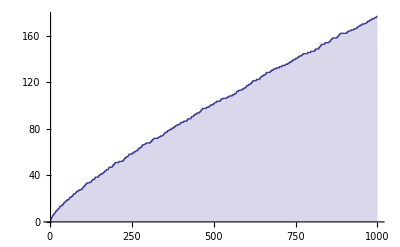

```mathematica
DiscretePlot[PP[n,1,1],{n,2,1000}]
```

```mathematica
DF[n_,a_] := PP[n,1,a]-PP[n-1,1,a]
```

```mathematica
Table[{n,DF[n,-I]},{n,1,100}] // TableForm
```

1 | 0
2 | -ⅈ
3 | -ⅈ
4 | 1/2-ⅈ
5 | -ⅈ
6 | 1-ⅈ
7 | -ⅈ
8 | 1-(2 ⅈ)/3
9 | 1/2-ⅈ
10 | 1-ⅈ
11 | -ⅈ
12 | 2
13 | -ⅈ
14 | 1-ⅈ
15 | 1-ⅈ
16 | 5/4
17 | -ⅈ
18 | 2
19 | -ⅈ
20 | 2
21 | 1-ⅈ
22 | 1-ⅈ
23 | -ⅈ
24 | 2+2 ⅈ
25 | 1/2-ⅈ
26 | 1-ⅈ
27 | 1-(2 ⅈ)/3
28 | 2
29 | -ⅈ
30 | 3+ⅈ
31 | -ⅈ
32 | 1+(4 ⅈ)/5
33 | 1-ⅈ
34 | 1-ⅈ
35 | 1-ⅈ
36 | 2+3 ⅈ
37 | -ⅈ
38 | 1-ⅈ
39 | 1-ⅈ
40 | 2+2 ⅈ
41 | -ⅈ
42 | 3+ⅈ
43 | -ⅈ
44 | 2
45 | 2
46 | 1-ⅈ
47 | -ⅈ
48 | 4 ⅈ
49 | 1/2-ⅈ
50 | 2
51 | 1-ⅈ
52 | 2
53 | -ⅈ
54 | 2+2 ⅈ
55 | 1-ⅈ
56 | 2+2 ⅈ
57 | 1-ⅈ
58 | 1-ⅈ
59 | -ⅈ
60 | 2+6 ⅈ
61 | -ⅈ
62 | 1-ⅈ
63 | 2
64 | 1/6+(4 ⅈ)/3
65 | 1-ⅈ
66 | 3+ⅈ
67 | -ⅈ
68 | 2
69 | 1-ⅈ
70 | 3+ⅈ
71 | -ⅈ
72 | -2+6 ⅈ
73 | -ⅈ
74 | 1-ⅈ
75 | 2
76 | 2
77 | 1-ⅈ
78 | 3+ⅈ
79 | -ⅈ
80 | 4 ⅈ
81 | 5/4
82 | 1-ⅈ
83 | -ⅈ
84 | 2+6 ⅈ
85 | 1-ⅈ
86 | 1-ⅈ
87 | 1-ⅈ
88 | 2+2 ⅈ
89 | -ⅈ
90 | 2+6 ⅈ
91 | 1-ⅈ
92 | 2
93 | 1-ⅈ
94 | 1-ⅈ
95 | 1-ⅈ
96 | -4+4 ⅈ
97 | -ⅈ
98 | 2
99 | 2
100 | 2+3 ⅈ